```mathematica
Series[-(1/2+x)Log[1+2x]-(1/2-x)Log[1-2x],{x,0,20}]
```

-2 x^2-(4 x^4)/3-(32 x^6)/15-(32 x^8)/7-(512 x^10)/45-(1024 x^12)/33-(8192 x^14)/91-(4096 x^16)/15-(131072 x^18)/153-(262144 x^20)/95+O[x]^21

```mathematica
Integrate[-Log[1+y]Exp[-t y^2/2],{y,-1,Infinity},Assumptions->{t>0}]
```

-HypergeometricPFQ[{1/2,1/2},{3/2,3/2},-t/2]-1/(4 √t)√π (√2 t HypergeometricPFQ[{1,1},{3/2,2},-t/2]-√2 (EulerGamma+Log[2 t]+Erf[(√t)/(√2)] (2 EulerGamma+Log[2 t]))+√t Hypergeometric1F1Regularized^(0,1,0)[1/2,3/2,-t/2])

```mathematica
Integrate[-y Log[1+y]Exp[-t y^2/2],{y,-1,Infinity},Assumptions->{t>0}]
```

-(ⅇ^(-t/2) (-EulerGamma+π Erfi[(√t)/(√2)]+Log[2]-Log[t]+Hypergeometric1F1^(1,0,0)[0,1/2,t/2]))/(2 t)

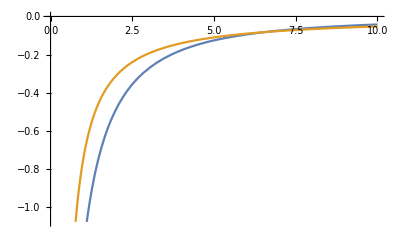

```mathematica
f[t_]:=-HypergeometricPFQ[{1/2,1/2},{3/2,3/2},-t/2]-1/(4 √t)√π (√2 t HypergeometricPFQ[{1,1},{3/2,2},-t/2]-√2 (EulerGamma+Log[2 t]+Erf[(√t)/(√2)] (2 EulerGamma+Log[2 t]))+√t Derivative[0,1,0][Hypergeometric1F1Regularized][1/2,3/2,-t/2])-1/(2 t)ⅇ^(-t/2) (-EulerGamma+π Erfi[(√t)/(√2)]+Log[2]-Log[t]+Derivative[1,0,0][Hypergeometric1F1][0,1/2,t/2]);
Plot[{f[x],-0.5/x-0.25/x^2},{x,0,10}]
```

```mathematica
Integrate[-Log[1-y]Exp[-t y^2/2],{y,-Infinity,1},Assumptions->{t>0}]
```

-HypergeometricPFQ[{1/2,1/2},{3/2,3/2},-t/2]-1/(4 √t)√π (√2 t HypergeometricPFQ[{1,1},{3/2,2},-t/2]-√2 (EulerGamma+Log[2 t]+Erf[(√t)/(√2)] (2 EulerGamma+Log[2 t]))+√t Hypergeometric1F1Regularized^(0,1,0)[1/2,3/2,-t/2])

```mathematica
Integrate[y Log[1-y]Exp[-t y^2/2],{y,-Infinity,1},Assumptions->{t>0}]
```

(ⅇ^(-t/2) (EulerGamma-π Erfi[(√t)/(√2)]+Log[t/2]-Hypergeometric1F1^(1,0,0)[0,1/2,t/2]))/(2 t)

```mathematica
g[t_]:=-HypergeometricPFQ[{1/2,1/2},{3/2,3/2},-t/2]-1/(4 √t)√π (√2 t HypergeometricPFQ[{1,1},{3/2,2},-t/2]-√2 (EulerGamma+Log[2 t]+Erf[(√t)/(√2)] (2 EulerGamma+Log[2 t]))+√t Derivative[0,1,0][Hypergeometric1F1Regularized][1/2,3/2,-t/2])+(ⅇ^(-t/2) (EulerGamma-π Erfi[(√t)/(√2)]+Log[t/2]-Derivative[1,0,0][Hypergeometric1F1][0,1/2,t/2]))/(2 t);
g[4.]
```

-0.177535